```mathematica
dataW=Import["D:\\data.DAT"]
Print["length of data:  ",%//Length]
```

{{300,0.024},{400,0.035},{500,0.046},{600,0.058},{700,0.067},{800,0.083},{900,0.097},{1000,0.111},{1100,0.125},{1200,0.14},{1300,0.155},{1400,0.17},{1500,0.186},{1600,0.202},{1700,0.219},{1800,0.235},{1900,0.252},{2000,0.269}}

length of data:  18

```mathematica
dataW//MatrixForm
```

(300 | 0.024
400 | 0.035
500 | 0.046
600 | 0.058
700 | 0.067
800 | 0.083
900 | 0.097
1000 | 0.111
1100 | 0.125
1200 | 0.14
1300 | 0.155
1400 | 0.17
1500 | 0.186
1600 | 0.202
1700 | 0.219
1800 | 0.235
1900 | 0.252
2000 | 0.269)

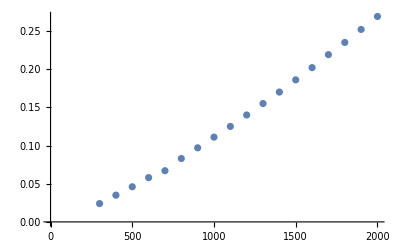

```mathematica
ListPlot[dataW]
```

```mathematica
e[T_]:=0.02424 (T/303.16)^(1.27591)
```

```mathematica
i=RandomInteger[{1,18}];
dataW[[i]][[1]]    (*温度*)
{dataW[[i]][[2]],(*辐射度数据*)e[dataW[[i]][[1]]]} (*辐射度经验值，即e(T)函数值*)
```

1000

{0.111,0.111141}

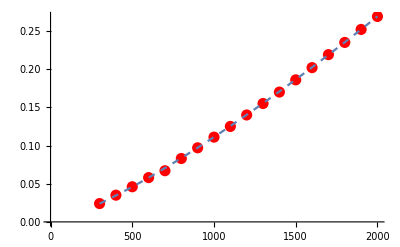

```mathematica
Show[ListPlot[dataW,PlotStyle->{Red,PointSize[0.02]}],Plot[e[T],{T,dataW[[1]][[1]],dataW[[18]][[1]]},PlotStyle->Dashed]]
```

```mathematica
Export["D:\\dataW.jpg",%]
```

D:\dataW.jpg